## CSV-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Warning: Cellzilla2D: xSSA.m not found in path. Some stochastic conversion functions may not work as expected. It should be loaded manually before any xSSA (stochastic) simulations can be run.

Cellzilla2D (3.0.51 (05 June 2017)) loaded Tue 6 Jun 2017 18:23:00
using xCellerator 0.95 and XSSA ** Not Found **
GPL License Terms Apply

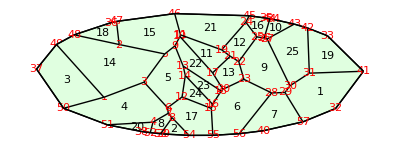

```mathematica
egg=TemplateRandomOvalish[25,{40,15}];
ShowTissue[egg, "CellNumbers"-> True, "VertexNumbers"-> Red]
```

```mathematica
CSVFile[egg,"egg-file-not-flat.csv"]
```

/Users/mathman/egg-file-not-flat.csv

```mathematica
CSVFile[egg,"egg-file-flat.csv"]
```

/Users/mathman/egg-file-flat.csv